# Visualisation of RiverSIM JSON files

## Import/Export

### Opens system dialog which looks only for JSON files.

```mathematica
OpenJSONDialog[]:=SystemDialogInput["FileOpen",{"simdata.json",{"RiverSim files"->{"*.json"}}}]
```

### By given file path(or files paths) returns JSON data as Association

```mathematica
ImportJSONData[filesPaths_]:=Module[{},
Switch[Head[filesPaths],
String,
Import[filesPaths,"RawJSON"],
List,

Import[#,"RawJSON"]&/@filesPaths
]
];
```

### Combines previous two function, using dialog import JSON as Mathematica association

```mathematica
OpenJSONData[]:=Module[{files},
files=OpenJSONDialog[];
ImportJSONData[files]
];
```

## Visualization

### Plots RiverSIM simulation trees, by giving an association of JSON file as an input

```mathematica
PlotSimData[data_, color_:Blue,legend_:"" , height_:{-1,-1}, width_:{-1,-1}]:=
ListPlot[
Flatten[
data["Trees"]["Branches"][[All,"coords"]],
{1}
],
Joined->True,
PlotRange->{
If[width=={-1,-1},{0,data["Model", "width"]},width],
If[height=={-1,-1},{0,data["Model", "height"]}, height]
}, 
AspectRatio->1, 
Joined->True,
PlotStyle->color,
PlotLegends->{legend},
AxesLabel->{"X","Y"},
ImageSize->Large
];
```

### Performance Visualization

```mathematica
PerformancePlot[simData_:Association]:=ListPlot[simData["RuntimeInfo","EachCycleTime"],Joined->True,AxesLabel->{"Number Of Steps", "Time"},ImageSize->Large]
```

### And combination of all above functions:

```mathematica
PlotJSONFile[color_:Blue,legend_:"" , height_:{-1,-1}, width_:{-1,-1}]:=Module[
{simData},
simData=OpenJSONData[];
Row[{
PlotSimData[simData,color, legend, height,width],
PerformancePlot[simData]
}]
]
```

# Example of usage

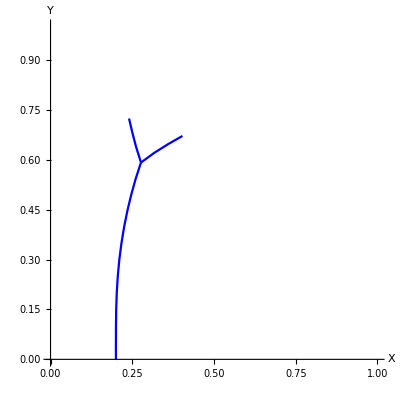

```mathematica
PlotJSONFile[]
```

```mathematica
simulationFilesPaths=OpenJSONDialog[]
```

{C:\Users\ofcra\Bin\riversim\laplacea_sample_river.json,C:\Users\ofcra\Bin\riversim\laplacea_sample_river_0.json,C:\Users\ofcra\Bin\riversim\laplacea_sample_river_1.json,C:\Users\ofcra\Bin\riversim\laplacea_sample_river_2.json,C:\Users\ofcra\Bin\riversim\laplacea_sample_river_3.json}

```mathematica
simAssoc = ImportJSONData[simulationFilesPaths];
```

```mathematica
sampleData=simAssoc[[1]]
```

<|Border→<|SomeDetails→Points and lines should be in counterclockwise order. SourcesIDs is array of pairs - where first number - is related branch id(source branche), and second is index of related point in coords array(after initialization it will be source point of related branch). Lines consist of three numbers: first and second - point index in coords array, third - configures boundary condition(See --boundary-condition option in program: ./riversim -h).,SourceIds→{{1,4}},coords→{{1.,0.},{1.,10.},{0.,10.},{0.,0.},{0.2,0.}},lines→{{0,1,1},{1,2,2},{2,3,3},{3,4,4},{4,0,4}}|>,Description→RiverSim simulation data and state of program. All coordinates are in normal cartesian coordinate system and by default are x > 0 and y > 0. Default values of simulation assumes that coordinates values will be of order 0 - 200. Greater values demands a lot of time to run, small are not tested(Problem of scalling isn't resolved yet TODO).,GeometryDifference→<|AlongBranches→{},BiffuractionPoints→{},Description→This structure holds info about backward river simulation. AlongBranches consist of five arrays for each branch: {branch_id: {1..}, {2..}, {3..}, {4..}, {5..}}, Where first consist of angles values allong branch(from tip to source), second - distance between tips, third - a(1) elements, forth - a(2) elements, fifth - a(3) elements. In case of --simulation-type=2, first item - integral value over whole region, second - disk integral over tip with r = 0.1, and rest are series params. BiffuractionPoints - is similar to previous object. It has same parameters but in biffurcation point. {source_branch_id: {lenght of non zero branch, which doesnt reached biffurcation point as its adjacent branch},{a(1)},{a(2)},{a(3)}}.|>,Model→<|Description→All model parameters. Almost all options are described in program options: ./riversim -h. riverBoundaryId - value of boundary id of river(solution equals zero on river boundary) ,Integration→<|exponant→2.,radius→0.03,weightRadius→0.01|>,Mesh→<|eps→1/1000000,exponant→7.,maxArea→100000.,maxEdge→1.,minAngle→30.,minArea→0.0001,minEdge→1/12500000,ratio→2.3,refinmentRadius→0.04,sigma→1.9,staticRefinmentSteps→3|>,Solver→<|adaptiveRefinmentSteps→0,iterationSteps→6000,quadratureDegree→3,refinmentFraction→0.1,tol→1/1000000000000|>,biffurcationAngle→0.628319,biffurcationMinDistance→0.05,biffurcationThreshold→-0.1,biffurcationThreshold2→0.001,biffurcationType→0,boundaryCondition→1,boundaryIds→{1,2,3,4},ds→0.01,dx→0.2,eta→1.,fieldValue→0.,growthMinDistance→0.01,growthThreshold→0.,growthType→0,height→10.,numberOfBackwardSteps→5,riverBoundaryId→4,width→1.|>,RuntimeInfo→<|Description→Units are in seconds.,EachCycleTime→{0.609375,1.34375,1.375,2.23438,1.84375,1.8125,2.35938,2.17188,1.96875,1.90625,1.9375,2.23438,1.96875,2.,1.875,1.85938,1.70313,2.54688,2.57813,2.29688,2.32813,2.51563,2.04688,1.98438,2.32813,2.57813,2.9375,2.39063,2.25,2.76563,2.92188,2.54688,3.53125,4.10938,3.17188,2.375,2.17188,2.14063,2.54688,3.5,2.57813,2.89063,2.92188,2.32813,2.65625,2.10938,2.4375,2.76563,2.48438,2.09375,2.28125,2.28125,2.42188,2.15625,2.09375,2.28125,2.3125,2.14063,2.39063,2.375,2.35938,2.5625,2.53125,2.67188,2.76563,2.8125,2.82813,3.1875,2.5625,2.5,3.40625,5.125,3.4375,3.9375,4.1875,2.54688,2.51563,2.8125,2.4375,2.26563,2.875,2.79688,2.29688,2.70313,2.26563,2.73438,2.5,2.70313,2.60938,2.64063,2.89063,2.85938,2.53125,2.4375,2.85938,2.6875,2.90625,2.85938,2.26563,2.84375,2.95313,2.32813,2.375,2.64063,2.92188,2.70313,2.8125,2.96875,2.64063,2.5,2.90625,2.9375,2.78125,2.5625,2.67188,2.45313,2.54688,2.6875,2.53125,2.54688,2.8125,2.75,2.54688,2.57813,3.01563,3.14063,2.78125,2.65625,2.96875,2.67188,3.07813,3.20313,2.84375,2.75,2.95313,2.85938,2.92188,2.8125,2.67188,3.04688,2.90625,3.20313,2.85938,2.71875,2.89063,2.6875,2.67188,2.98438,3.26563,3.23438,3.32813,2.9375,3.09375,3.04688,3.03125,2.71875,2.875,2.5625,3.04688,3.15625,2.45313,2.78125,2.73438,3.26563,3.17188,2.82813,2.79688,3.07813,2.96875,2.9375,3.01563,3.07813,2.89063,3.07813,3.375,3.0625,3.23438,3.34375,2.9375,3.,3.03125,2.90625,3.21875,3.53125,2.73438,2.70313,4.42188,3.14063,3.32813,3.1875,3.26563,3.85938,2.96875,3.89063,3.64063,3.89063,3.46875,4.10938,3.45313,3.28125,3.09375,3.51563,2.90625,2.92188,3.57813,3.60938,3.4375,3.98438,3.,3.32813,3.89063,3.34375,3.39063,2.95313,3.25,3.21875,2.98438,3.39063,3.40625,3.29688,3.25,3.10938,3.32813,3.73438,3.96875,3.20313,3.82813,2.96875,3.5625,2.96875,3.40625,3.32813,3.65625,2.96875,4.07813,3.60938,3.5,3.84375,4.,3.54688,3.40625,3.60938,3.5625,3.125,3.78125,3.92188,3.67188,4.26563,3.64063,4.20313,3.32813,3.6875,3.5,3.51563,3.57813,3.65625,3.42188,4.42188,3.5625,3.65625,3.625,3.625,3.48438,3.5625,3.60938,3.5625,3.75,3.625,3.64063,3.9375,3.46875,3.42188,4.28125,4.04688,3.84375,3.85938,3.76563,4.07813,3.73438,4.53125,4.09375,3.96875,4.,3.95313,3.89063,3.9375,3.9375,3.76563,3.78125,3.96875,4.5625,4.04688,3.82813,3.75,4.04688,3.67188,4.59375,3.98438,3.95313,4.,3.95313,3.9375,3.76563,3.67188,4.60938,3.82813,4.14063,4.6875,4.32813,4.6875,4.29688,4.75,4.40625,3.78125,4.67188,4.59375,4.04688,3.82813,3.82813,4.4375,3.92188,3.6875,2.79688,3.6875,4.04688,4.95313,3.9375,3.92188,4.64063,3.70313,3.6875,4.15625,3.95313,4.45313,4.42188,4.67188,4.73438,4.60938,4.15625,4.29688,4.125,4.5625,4.23438,4.21875,4.3125,4.625,4.35938,4.78125,4.51563,4.5625,4.4375,5.71875,6.96875,5.5,5.25,4.5625,4.48438,4.67188,4.71875,4.42188,4.73438,6.32813,6.875,4.6875,4.57813,4.89063,4.48438,5.0625,4.53125,4.53125,4.51563,4.64063,5.60938,4.59375,6.70313,7.85938,5.07813,4.6875,4.8125,4.875,7.96875,5.14063,4.875,4.90625,4.46875,4.98438,5.25,5.03125,4.25,6.32813,7.53125,7.26563,4.73438,4.92188,4.84375,4.71875,5.25,5.14063},EndDate→Wed Dec 11 18:21:23 2019
,InputFile→,MaximalRiverHeight→100.,NumberOfSteps→1000,StartDate→Wed Dec 11 18:08:30 2019
,TotalTime→1378.77|>,Trees→<|Branches→{<|Desciption→Order of elements should be from source point to tip. Source point should be the same as first point of array. Source angle - represents branch growth dirrection when it consist only from one(source) point. For example perpendiculary to border line. Id should be unique(and >= 1) to each branch and is referenced in Trees->Relations structure and Border->SourcesId,coords→{{0.2,0.},{0.200004,0.01},{0.200005,0.02},{0.20001,0.03},{0.200015,0.04},{0.200024,0.05},{0.200039,0.06},{0.200062,0.07},{0.200101,0.0799999},{0.200162,0.0899997},{0.20024,0.0999994},{0.200342,0.109999},{0.200467,0.119998},{0.200626,0.129997},{0.200815,0.139995},{0.20104,0.149993},{0.20131,0.159989},{0.20162,0.169984},{0.201975,0.179978},{0.202375,0.18997},{0.202834,0.199959},{0.203348,0.209946},{0.203917,0.21993},{0.20454,0.22991},{0.205219,0.239887},{0.205947,0.249861},{0.206727,0.25983},{0.20756,0.269796},{0.208445,0.279756},{0.209382,0.289712},{0.21037,0.299663},{0.211404,0.30961},{0.212494,0.31955},{0.213633,0.329485},{0.214819,0.339415},{0.216047,0.349339},{0.217321,0.359257},{0.218639,0.36917},{0.220005,0.379076},{0.221407,0.388978},{0.222845,0.398874},{0.224321,0.408764},{0.225839,0.418648},{0.227392,0.428527},{0.228979,0.4384},{0.230602,0.448268},{0.232255,0.45813},{0.233937,0.467988},{0.235647,0.47784},{0.237384,0.487688},{0.239145,0.497532},{0.240934,0.507371},{0.242753,0.517204},{0.244598,0.527032},{0.246466,0.536856},{0.248349,0.546677},{0.250246,0.556496},{0.25216,0.566311},{0.254087,0.576123},{0.256029,0.585933},{0.257988,0.595739},{0.259965,0.605542},{0.261952,0.615342},{0.263947,0.625141},{0.265953,0.634938},{0.26797,0.644733},{0.269994,0.654526},{0.272033,0.664316},{0.274081,0.674104},{0.276139,0.68389},{0.278194,0.693676},{0.280252,0.703462},{0.282315,0.713247},{0.284373,0.723033},{0.286437,0.732818},{0.288501,0.742602},{0.290566,0.752387},{0.292629,0.762172},{0.294693,0.771956},{0.296747,0.781743},{0.298798,0.791531},{0.300851,0.801318},{0.302899,0.811106},{0.304948,0.820893},{0.306994,0.830682},{0.309033,0.840472},{0.311067,0.850263},{0.313094,0.860055},{0.315114,0.869849},{0.317128,0.879644},{0.319134,0.889441},{0.321139,0.899238},{0.323132,0.909037},{0.325111,0.918839},{0.327077,0.928644},{0.329031,0.938451},{0.330983,0.948259},{0.33293,0.958068},{0.334867,0.967878},{0.336792,0.977691},{0.338698,0.987508},{0.340591,0.997327},{0.342473,1.00715},{0.344338,1.01697},{0.346196,1.0268},{0.348047,1.03663},{0.349889,1.04645},{0.351722,1.05629},{0.353546,1.06612},{0.35535,1.07595},{0.357145,1.08579},{0.358928,1.09563},{0.360699,1.10547},{0.362458,1.11532},{0.364197,1.12516},{0.36592,1.13502},{0.36763,1.14487},{0.369324,1.15472},{0.371007,1.16458},{0.372673,1.17444},{0.374318,1.1843},{0.375945,1.19417},{0.377555,1.20404},{0.379147,1.21391},{0.380729,1.22379},{0.382295,1.23366},{0.383851,1.24354},{0.385387,1.25342},{0.38691,1.26331},{0.388417,1.27319},{0.389909,1.28308},{0.391391,1.29297},{0.392862,1.30286},{0.394316,1.31276},{0.395759,1.32265},{0.397184,1.33255},{0.39859,1.34245},{0.399978,1.35235},{0.401351,1.36226},{0.402709,1.37217},{0.404054,1.38207},{0.405383,1.39199},{0.406696,1.4019},{0.407991,1.41181},{0.409268,1.42173},{0.410533,1.43165},{0.411779,1.44157},{0.41301,1.4515},{0.414226,1.46142},{0.415437,1.47135},{0.416629,1.48128},{0.41781,1.49121},{0.418971,1.50114},{0.420123,1.51108},{0.421256,1.52101},{0.42238,1.53095},{0.423488,1.54089},{0.424584,1.55083},{0.42567,1.56077},{0.426743,1.57071},{0.427798,1.58065},{0.428839,1.5906},{0.429866,1.60055},{0.430883,1.61049},{0.431887,1.62044},{0.432873,1.63039},{0.433843,1.64035},{0.434803,1.6503},{0.435754,1.66026},{0.436692,1.67021},{0.437619,1.68017},{0.438533,1.69013},{0.439439,1.70009},{0.440334,1.71005},{0.441216,1.72001},{0.442091,1.72997},{0.44295,1.73993},{0.443803,1.7499},{0.444647,1.75986},{0.445477,1.76982},{0.446297,1.77979},{0.447109,1.78976},{0.447905,1.79973},{0.448694,1.8097},{0.449468,1.81967},{0.450237,1.82964},{0.450991,1.83961},{0.451733,1.84958},{0.452464,1.85955},{0.453183,1.86953},{0.453896,1.8795},{0.454597,1.88948},{0.455288,1.89945},{0.45597,1.90943},{0.456642,1.91941},{0.457306,1.92939},{0.457959,1.93936},{0.458604,1.94934},{0.45924,1.95932},{0.459869,1.9693},{0.46049,1.97928},{0.4611,1.98927},{0.461699,1.99925},{0.462287,2.00923},{0.462866,2.01921},{0.463439,2.0292},{0.464006,2.03918},{0.464566,2.04916},{0.465112,2.05915},{0.465657,2.06913},{0.466192,2.07912},{0.466719,2.08911},{0.467234,2.09909},{0.467749,2.10908},{0.468258,2.11907},{0.468757,2.12905},{0.469245,2.13904},{0.469724,2.14903},{0.470194,2.15902},{0.47066,2.16901},{0.471118,2.179},{0.471574,2.18899},{0.472027,2.19898},{0.472476,2.20897},{0.472914,2.21896},{0.473346,2.22895},{0.473768,2.23894},{0.474184,2.24893},{0.474593,2.25892},{0.474999,2.26892},{0.475392,2.27891},{0.475783,2.2889},{0.47617,2.29889},{0.476548,2.30889},{0.476916,2.31888},{0.47728,2.32887},{0.477637,2.33887},{0.47799,2.34886},{0.478337,2.35885},{0.478675,2.36885},{0.479005,2.37884},{0.479334,2.38884},{0.479654,2.39883},{0.479972,2.40883},{0.480288,2.41882},{0.480598,2.42882},{0.480905,2.43881},{0.481201,2.44881},{0.481497,2.4588},{0.481783,2.4688},{0.482069,2.47879},{0.482348,2.48879},{0.482631,2.49879},{0.482909,2.50878},{0.48318,2.51878},{0.483445,2.52878},{0.483709,2.53877},{0.483968,2.54877},{0.484222,2.55877},{0.48447,2.56876},{0.484713,2.57876},{0.484949,2.58876},{0.485181,2.59875},{0.485417,2.60875},{0.485649,2.61875},{0.485878,2.62875},{0.486103,2.63874},{0.486328,2.64874},{0.486545,2.65874},{0.486761,2.66874},{0.486976,2.67873},{0.487186,2.68873},{0.487394,2.69873},{0.487599,2.70873},{0.487796,2.71873},{0.48799,2.72872},{0.488176,2.73872},{0.488364,2.74872},{0.48855,2.75872},{0.488729,2.76872},{0.488913,2.77872},{0.489091,2.78871},{0.489264,2.79871},{0.489432,2.80871},{0.489599,2.81871},{0.489763,2.82871},{0.489923,2.83871},{0.490088,2.84871},{0.49025,2.8587},{0.490406,2.8687},{0.490561,2.8787},{0.490716,2.8887},{0.490861,2.8987},{0.491006,2.9087},{0.491155,2.9187},{0.491301,2.9287},{0.491444,2.9387},{0.491582,2.94869},{0.491718,2.95869},{0.491849,2.96869},{0.491974,2.97869},{0.492096,2.98869},{0.492222,2.99869},{0.49234,3.00869},{0.492459,3.01869},{0.492578,3.02869},{0.492695,3.03869},{0.492811,3.04869},{0.492925,3.05869},{0.49304,3.06869},{0.493154,3.07868},{0.493261,3.08868},{0.493367,3.09868},{0.49347,3.10868},{0.493574,3.11868},{0.493677,3.12868},{0.493777,3.13868},{0.493876,3.14868},{0.493966,3.15868},{0.494056,3.16868},{0.494145,3.17868},{0.494234,3.18868},{0.494323,3.19868},{0.494414,3.20868},{0.494503,3.21868},{0.494592,3.22868},{0.494681,3.23868},{0.494776,3.24868},{0.494868,3.25868},{0.494955,3.26868},{0.495041,3.27868},{0.49513,3.28868},{0.495215,3.29868},{0.495292,3.30867},{0.495368,3.31867},{0.495442,3.32867},{0.495512,3.33867},{0.495583,3.34867},{0.495652,3.35867},{0.495715,3.36867},{0.495774,3.37867},{0.495832,3.38867},{0.495893,3.39867},{0.495955,3.40867},{0.496016,3.41867},{0.496074,3.42867},{0.496125,3.43867},{0.496172,3.44867},{0.496222,3.45867},{0.496267,3.46867},{0.496314,3.47867},{0.496359,3.48867},{0.496401,3.49867},{0.496441,3.50867},{0.496476,3.51867},{0.496512,3.52867},{0.496545,3.53867},{0.496579,3.54867},{0.496613,3.55867},{0.496651,3.56867},{0.496684,3.57867},{0.49672,3.58867},{0.496757,3.59867},{0.496794,3.60867},{0.496827,3.61867},{0.496868,3.62867},{0.496913,3.63867},{0.496949,3.64867},{0.496984,3.65867},{0.497017,3.66867},{0.497047,3.67867},{0.497073,3.68867},{0.497103,3.69867},{0.497132,3.70867},{0.497163,3.71867},{0.497194,3.72867},{0.497225,3.73867},{0.497255,3.74867},{0.497285,3.75867},{0.497314,3.76867},{0.497344,3.77867},{0.497369,3.78867},{0.497397,3.79867},{0.497421,3.80867},{0.497444,3.81867},{0.497466,3.82867},{0.497489,3.83867},{0.497511,3.84867},{0.497538,3.85867},{0.497562,3.86867},{0.497589,3.87867},{0.497621,3.88867},{0.49765,3.89867},{0.497672,3.90867},{0.497696,3.91867},{0.49772,3.92867},{0.497744,3.93867},{0.497768,3.94867},{0.497791,3.95867}},id→1,sourceAngle→1.5708,sourcePoint→{0.2,0.}|>},Description→SourcesIds represents sources(or root) branches of each rivers(yes you can setup several rivers in one run). Relations is array{...} of next elements {source_branch_id, {left_child_branch_id, right_child_branch_id} it holds structure of river divided into separate branches. Order of left and right id is important.,Relations→{},SourceIds→{1}|>,Version→2.6.0|>

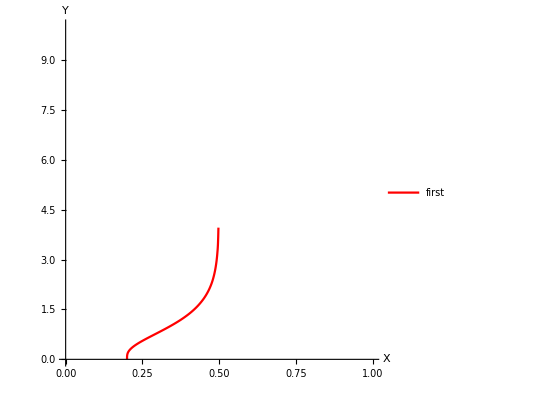

```mathematica
PlotSimData[sampleData, Red, {"first", "second", "third"}]
```

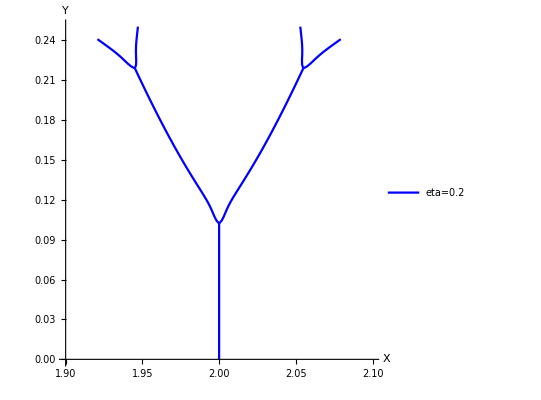
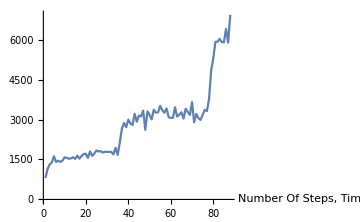

```mathematica
PlotJSONFile[Blue,"eta=0.2" ,{0,0.25},{1.9,2.1}]
```

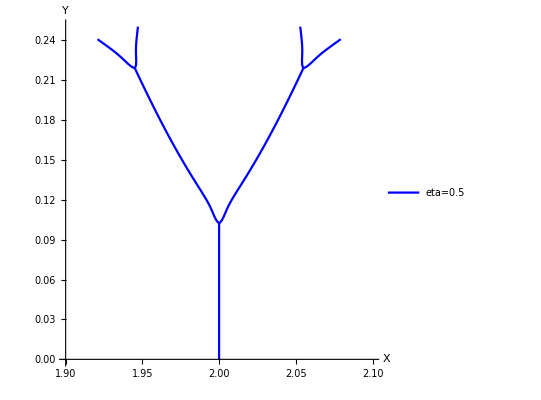
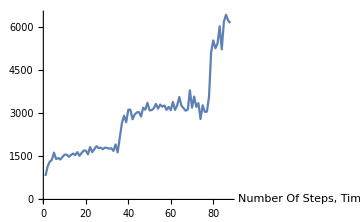

```mathematica
PlotJSONFile[Blue,"eta=0.5" ,{0,0.25},{1.9,2.1}]
```

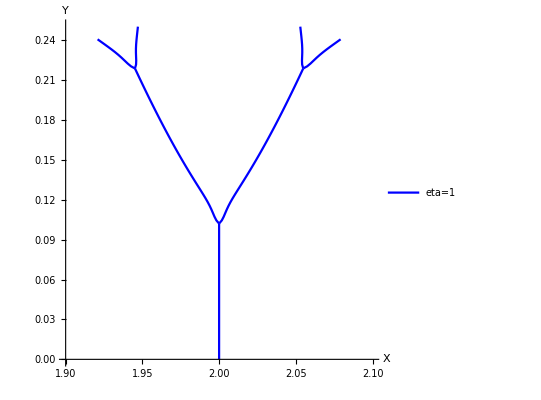
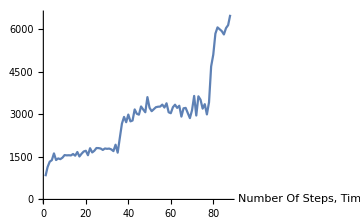

```mathematica
PlotJSONFile[Blue,"eta=1" ,{0,0.25},{1.9,2.1}]
```

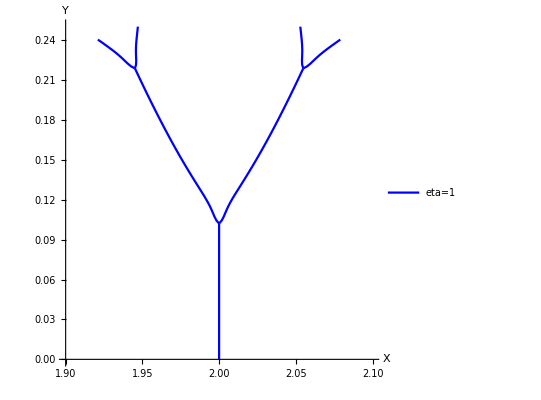
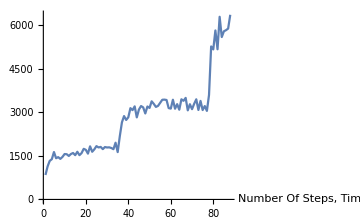

```mathematica
PlotJSONFile[Blue,"eta=1" ,{0,0.25},{1.9,2.1}]
```

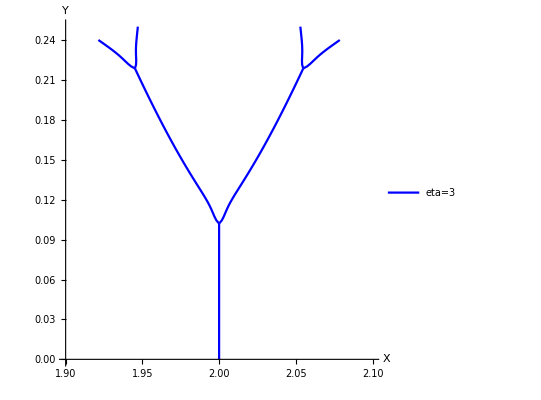
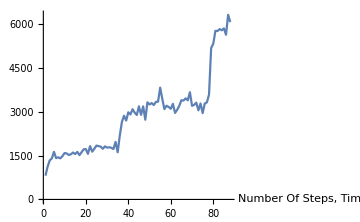

```mathematica
PlotJSONFile[Blue,"eta=3" ,{0,0.25},{1.9,2.1}]
```

# Dev Section

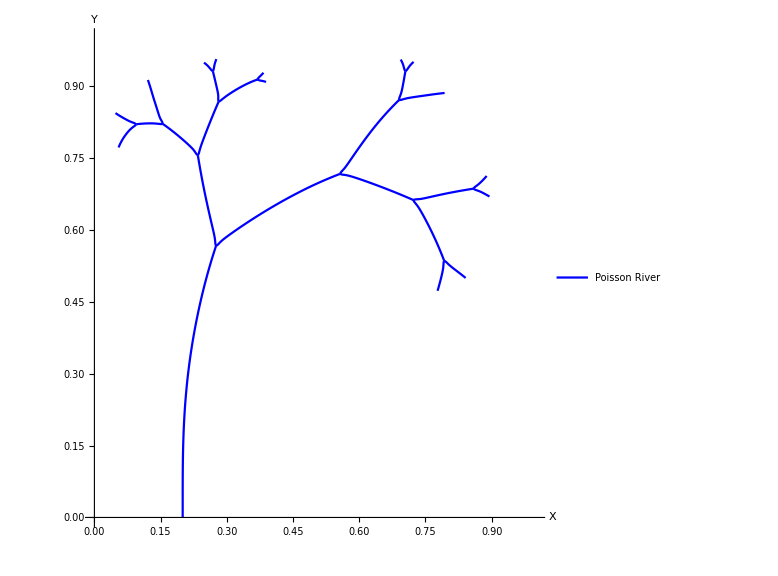
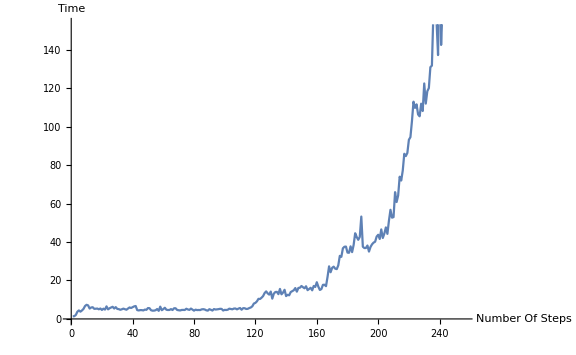

```mathematica
PlotJSONFile[Blue,"Poisson River"]
```